### Turing machine->Hypergraph

n is the start point ). m is the thing we want

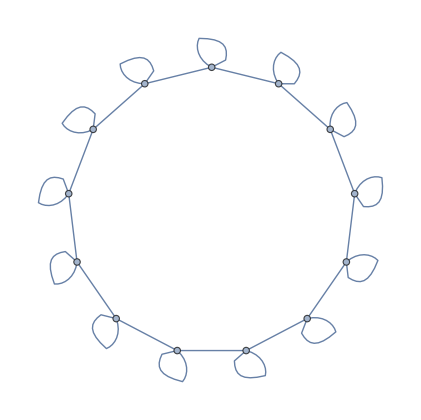

```mathematica
Graph[stateGraph[10]]
```

```mathematica
alphabetGraphHelper[n_]:= If[n ==0, {{1,1}},If[n==1,{{1,2},{2,1}}, Module[{x},x = Last[#][[1]]&[alphabetGraphHelper[n-1]]; Join[Drop[#,-1],{{x,x+1},{x+1,1}}]&[alphabetGraphHelper[n-1]]]]]
```

```mathematica
alphabetGraph[n_]:=If[n==0,{{1,1},{1,2}},Append[alphabetGraphHelper[n],{1,n+2}]]
```

```mathematica
graphToHypergraph[g_]:= g /. (x_Integer<->y_Integer -> {x,y})
```

Note that offset is either 1 or -1 or 0. Note that we expect the links to always be in that direction.

```mathematica
JoinState[n_,m_,stateF_]:= Join[ReplaceAll[stateGraph[stateF],Table[i->n+i,{i,1,stateF + 3}]],{{stateF + 3+n ,m }}]
```

join stateF with start value (x--the loop) and attach it to x+1. The x+1 should be connected to the zero alphabet. Note that the self loop should disappear from the original. join symbol F with start value stateF +  3 + x and attch it to x itsef.

```mathematica
concatenategraphs[g1_,g2_]:= graphToHypergraph[Join[{Max[VertexList[g1]]<->Max[VertexList[#]]},#]]&[EdgeList[GraphDisjointUnion[g1,g2]]]
```

```mathematica
concatenategraphsmin[g1_,g2_]:= graphToHypergraph[Join[{Min[VertexList[g1]]<->Max[VertexList[#]]},#]]&[EdgeList[GraphDisjointUnion[g1,g2]]]
```

```mathematica
initialWordToHypergraphHelper[word_List,acc_]:=If[word == {},acc,initialWordToHypergraphHelper[Drop[word,1],concatenategraphs[acc, alphabetGraph[word[[1]]]] ]]
```

```mathematica
initialWordToHypergraph[word_List]:= initialWordToHypergraphHelper[Drop[word,1],concatenategraphs[stateGraph[0],alphabetGraph[word[[1]]]]]
```

```mathematica
initialTapeToHypergraph[word_List]:=
Module[{x,y,z},
x = initialWordToHypergraph[word];
y = Max[VertexList[concatenategraphs[stateGraph[0],alphabetGraph[word[[1]]]]]];
z =  Max[VertexList[x]];
Join[x,{{y,z+1,z+2},{z,z+3,z+4,z+5}}]
]
```

The y and z are just to attach the hyperedge loops to recognize the ends of the tape. this is easy stuff

```mathematica
RulePlot[ResourceFunction["WolframModel"][TuringRule[{0,1}->{1,0}]]]
```

RulePlot::invalidRules: The rule specification TuringRule[{0,1}→{1,0}] should be either a Rule, RuleDelayed, or a List of them.

RulePlot[WolframModel[TuringRule[{0,1}→{1,0}]]]

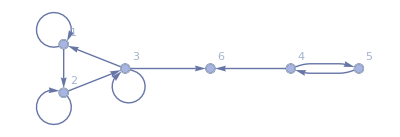

```mathematica
ResourceFunction["WolframModelPlot"][concatenategraphs[stateGraph[0],alphabetGraph[1]],VertexLabels->Automatic]
```

```mathematica
Join[stateGraph[stateF]/.Table[i->n+i,{i,1,stateF+3}],{{stateF+3+n,m}}]
```

Table::iterb: Iterator {i,1,3+stateF} does not have appropriate bounds.

Table::iterb: Iterator {i,1,2+stateF} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Join::heads: Heads Table and List at positions 1 and 3 are expected to be the same.

ReplaceAll::reps: {Table[i→n+i,{i,1,3+stateF}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and List at positions 1 and 2 are expected to be the same.

Join[Join[Table[{i,i},{i,1,3+stateF}],Table[{i,i+1},{i,1,2+stateF}],{{3+stateF,1}}]/.Table[i→n+i,{i,1,3+stateF}],{{3+n+stateF,m}}]

```mathematica
JoinState[6,6,1]
```

{{7,7},{8,8},{9,9},{10,10},{7,8},{8,9},{9,10},{10,7},{10,6}}

```mathematica
JoinAlphabet[n_,m_,symbolF_]:= If[symbolF == 0,{{n+1,n+1},{n+1,m}} ,Join[ReplaceAll[alphabetGraphHelper[symbolF],Table[i-> n+ i,{i,1,symbolF + 1}]],{{n + symbolF + 1, m }}]]
```

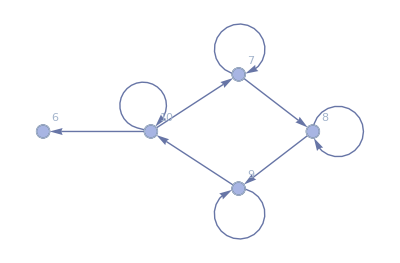

```mathematica
ResourceFunction["WolframModelPlot"][JoinState[6,6,1],VertexLabels->Automatic]
```

```mathematica
Graph[alphabetGraph[1]]
```

-Graphics-

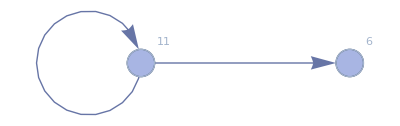

```mathematica
ResourceFunction["WolframModelPlot"][JoinAlphabet[10,6,0],VertexLabels->Automatic]
```

```mathematica
Information[JoinState]
```

```mathematica
TuringRule[{stateI_,symbolI_}-> {stateF_, symbolF_}]:= {#->  Join[
JoinState[Max[VertexList[#]],Max[VertexList[#]],stateF],JoinAlphabet[stateF + 3 + Max[VertexList[#]],Max[VertexList[#]], symbolF]]}&[concatenategraphs[stateGraph[stateI],alphabetGraph[symbolI]]]
```

```mathematica
TuringRule[{stateI_,symbolI_}-> {stateF_, symbolF_,offset_}]:= If[offset == 0, TuringRule[{stateI,symbolI}-> {stateF, symbolF}],
Module[ {x = Max[VertexList[#]]},
If[offset == 1, (*the edge cases---literally*)
{Join[#,{{x, x + 1}}] ->Join[JoinState[x + 1,x + 1,stateF],JoinAlphabet[stateF + 3 + x+1,x,symbolF],{{x, x + 1}}], Join[#,{{x ,  x+1, x+2, x+3}}] -> Join[JoinState[x+4,x+4,stateF],JoinAlphabet[stateF + 3 + x+4, x,symbolF],JoinAlphabet[stateF + 3+x +4+ symbolF+2 ,x+4,0],{{x,x+4},{x+4,x+4+stateF+3+symbolF+6,x+4+stateF+3+symbolF+7,x+4+stateF+3+symbolF+8}}]},
If[offset == -1, {Join[#,{{x+1, x }}] ->Join[JoinState[x + 1,x + 1,stateF],JoinAlphabet[stateF + 3 +x+1,Max[VertexList[#]],symbolF],{{x+1, x }}],
Join[#,{{x,x+1,x+2}}] ->Join[
JoinState[x+5,x+3,stateF],(*join the state at x+3*)JoinAlphabet[stateF + 3 + x+5, x,symbolF],(**)JoinAlphabet[stateF + 3+x +5+ symbolF+2 ,x+3,0],{{x+3,x},{x+3,x+4, x+5}}]
}]
]]&[concatenategraphs[stateGraph[stateI],alphabetGraph[symbolI]]]]
```

something wrong with turing rule with 0

```mathematica
HaltRule[state_]:= (Join[#,{{1,Max[VertexList[#]] + 1}}]-> {})&[stateGraph[state]]
```

So, the edge will be danglinG. sO JUST REDUCES TO TEH VERTEX.

```mathematica
tRexToHRex[list_]:= list  /. {({a_,b_}-> {c_,d_,e_}) ->({a+1,b}-> {c+1,d,e}), ({a_,b_}-> {c_,d_}) ->({a+1,b}-> {c+1,d}) }
```

```mathematica
HaltRule[10]
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,1},{1,14}}→{}

```mathematica
TuringToHypergraph[rules_,qHalt_,word_]:=ResourceFunction["WolframModel"][Join[Flatten[TuringRule/@rules,1],{HaltRule[qHalt]}],initialTapeToHypergraph[word],50,"EventsStatesPlotsList"]
```

This shoudl work

```mathematica
TuringMachinePlot
```

TuringMachinePlot

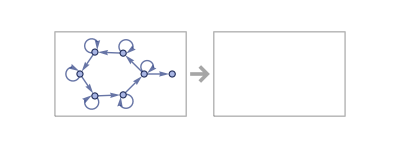

```mathematica
RulePlot[ResourceFunction["WolframModel"][HaltRule[3]]]
```

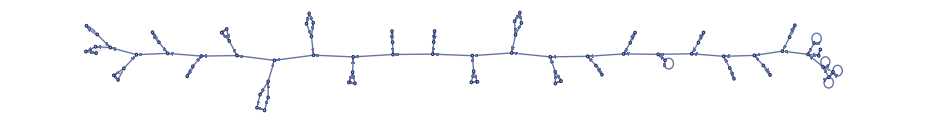

```mathematica
ResourceFunction["WolframModelPlot"][initialTapeToHypergraph[{0,1,1,1,1,0,1,1,2,3,2,1,1,2,3,4,2,1,1,2,1}]]
```

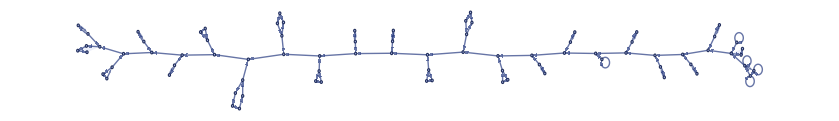

```mathematica
ResourceFunction["WolframModelPlot"][initialTapeToHypergraph[{0,1,1,1,1,0,1,1,2,3,2,1,1,2,3,4,2,1,1,2,1}]]
```

```mathematica
IsomorphicHypergraphQ[%653,%668]
```

IsomorphicHypergraphQ::invalidHypergraph: The argument at position 1 in IsomorphicHypergraphQ[%653,%668] is not a valid hypergraph.

IsomorphicHypergraphQ[%653,%668]

```mathematica
ResourceFunction["WolframHausdorffDimension"][initialTapeToHypergraph[{0,1,1,1,1,0,1,1,2,3,2,1,1,2,3,4,2,1,1,2,1}],1,"Dimension"]
```

[{{73,76},{69,73},{66,69},{63,66},{59,63},{53,59},{48,53},{44,48},{41,44},{38,41},{34,38},{29,34},{25,29},{22,25},{19,22},{17,19},{14,17},{11,14},{8,11},{5,8},{3,5},{1,1},{2,2},{3,3},{1,2},{2,3},{3,1},{4,4},{4,5},{6,7},{7,6},{6,8},{9,10},{10,9},{9,11},{12,13},{13,12},{12,14},{15,16},{16,15},{15,17},{18,18},{18,19},{20,21},{21,20},{20,22},{23,24},{24,23},{23,25},{26,27},{27,28},{28,26},{26,29},{30,31},{31,32},{32,33},{33,30},{30,34},{35,36},{36,37},{37,35},{35,38},{39,40},{40,39},{39,41},{42,43},{43,42},{42,44},{45,46},{46,47},{47,45},{45,48},{49,50},{50,51},{51,52},{52,49},{49,53},{54,55},{55,56},{56,57},{57,58},{58,54},{54,59},{60,61},{61,62},{62,60},{60,63},{64,65},{65,64},{64,66},{67,68},{68,67},{67,69},{70,71},{71,72},{72,70},{70,73},{74,75},{75,74},{74,76},{5,77,78},{76,79,80,81}},1,Dimension]

Fix error later.

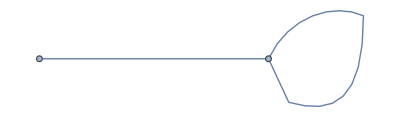

```mathematica
Graph[alphabetGraph[0]]
```

there’s an error her, fix it

```mathematica
alphabetGraph[0]
```

{{1,1},{1,2}}

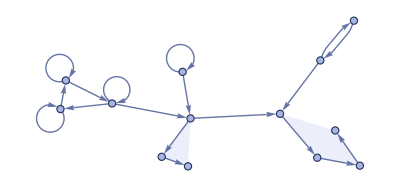

```mathematica
ResourceFunction["WolframModelPlot"][initialTapeToHypergraph[{0,1}]]
```

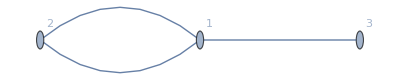

```mathematica
Graph[alphabetGraph[1],VertexLabels->Automatic]
```

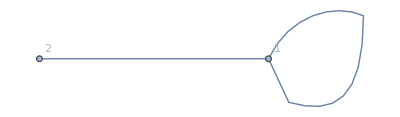

```mathematica
Graph[alphabetGraph[0],VertexLabels->Automatic]
```

This rule is a problem

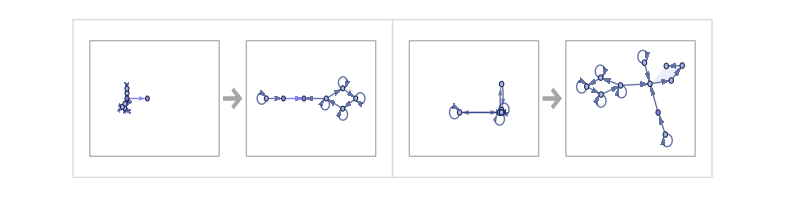

```mathematica
RulePlot[ResourceFunction["WolframModel"][TuringRule[{0,1}->{1,0,1}]]]
```

Busy beaver problem..

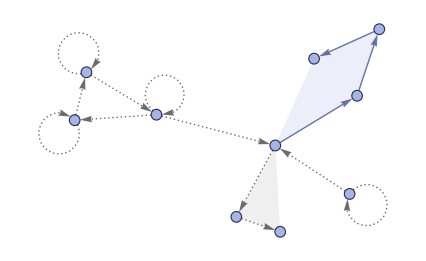
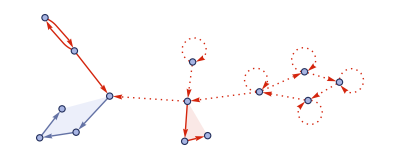
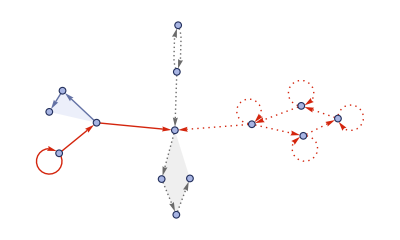
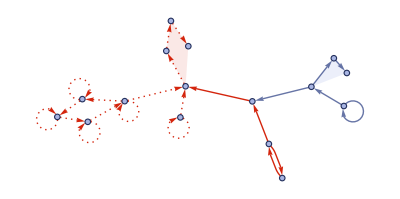
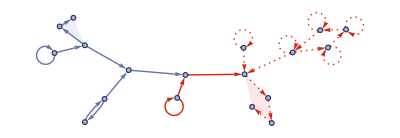
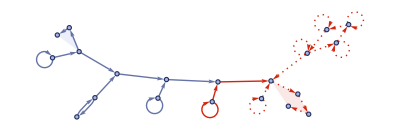
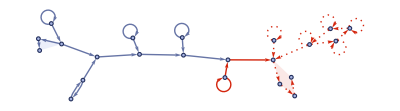
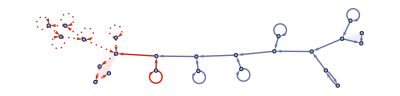
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TuringToHypergraph[{{0,1}->{3,0},{0,0}->{1,1,-1},{1,1}->{1,1,1},{1,0}->{1,0,1}},2,{0}]
```

### Multiway Turing -> Hypergraph

Ok, this might be fun.

My model is perfect, cannot be better. We are doing the exact same thing.. It also adds things.

What can we mean by the optimal model? Well, there’s a reason why hyeprgraph rewriting is better than turing machine and other rewrite rules. There’s a reason. Obviously, hypergraph rewriting can emulate turing machines very easily. And it has infinite memory. Maybe it can emulate tag systems and other systems like those...

Well, wll there’s maybe non-linear models fo computation.

Ok, let’s do this

```mathematica
MultiwayTuringToHypergraph[rules_,qHalt_,word_]:=
ResourceFunction["MultiwaySystem"]["WolframModel"->ResourceFunction["CanonicalWolframModelRule"][Join[Flatten[TuringRule/@rules,1],{HaltRule[qHalt]}]],{initialTapeToHypergraph[word]},1,"StatesGraph",VertexSize->1];
```

```mathematica
MultiwayTuringToHypergraph[{{0,1}->{0,0},{0,0}->{1,1,1},{0,0}->{1,1,-1},{1,1}->{1,1,1},{1,0}->{1,0,1}},2,{0}]
```

$Aborted

So this works.

However, the question is that can there be less rules to imokemenet the same turing machine. Well, maybe. Maybe there are mutliple rules athat are being aplpied at the same time..imporves the comptuatiobl pwere adn can be done in a few steps. For exampke, just like a register machine mgith be able to do things must faster than the  turing machine, therat;’s cuzz it
s a more powerful way of comptuign. So , there must be a alwa an alaogus way, right!

It is very hard to do that thing when we’re just givena  turing amchein, rigth? Because we don’t know from the  heaviour of thruing machien that what it does???

However, lambda calculus is a much better model. So let’s do that becaus eit is much better that way. I mean, lambda calculus is a rpograming lagnuage! Yes
There is a reason why it is harder to go from a register machine to algorithm than algorithm to reisger machine. This is because it is low level and each operation takes many steps. That is also the lambda calculus btw because numbers are binary naturals which are quite complex./

So yeah, things are simialr to the other.

I think that hypergraph rewiritn is powerful. So it must be the case that it will be like a higher model; of computation., Yes, I need to see all that. Hypegraph rewriting is non-linear in that sense. Well, note that we can study about computable numbers and stuff. That’ll be fun!

I think there are many possible mutliway systems can be generated.

### Tests

So in my model, the initiial state is 0 and the the head is initially at the starting state.

```mathematica
Turing
```

```mathematica
tRexToHRex[{{1,1}->{2,0,-1},{1,0}->{2,1,1},{2,1}->{1,0,1},{2,0}->{1,1,-1}}]
```

{{2,1}→{3,0,-1},{2,0}→{3,1,1},{3,1}→{2,0,1},{3,0}→{2,1,-1}}

Let’s do this...so for each offset rule, we will have 2 cases.

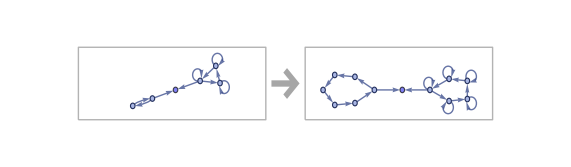

```mathematica
RulePlot[ResourceFunction["WolframModel"][TuringRule[{0,1}->{2,5}]]]
```

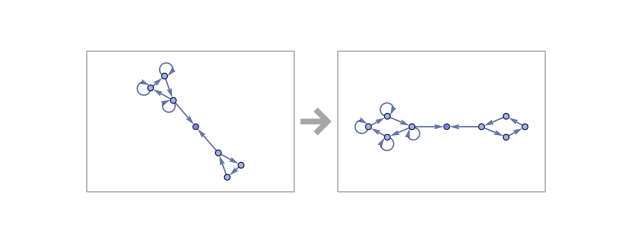

```mathematica
RulePlot[ResourceFunction["WolframModel"][TuringRule[{0,2}->{1,3}]]]
```

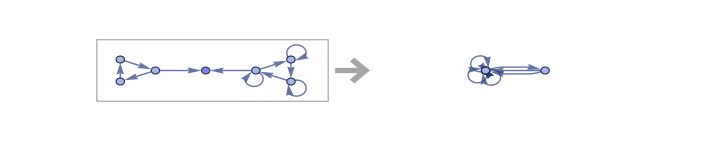

The only thing that matters is the pattern..no one cars...So yeah. So how to do this? Well, we start with the simple pattern.

concatenategraphs[stateGraph2[0], alphabetGraph[1]] where we have to pivot on the point.

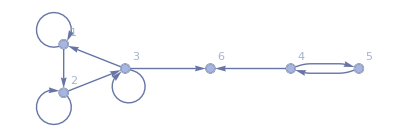

```mathematica
ResourceFunction["WolframModelPlot"][concatenategraphs[stateGraph2[0],alphabetGraph[1],3,3],VertexLabels->Automatic]
```

```mathematica
ResourceFunction["WolframModelPlot"][concatenategraphs[stateGraph2[0],alphabetGraph[1]],VertexLabels->Automatic]
```

-Graphics-

### Turing

Definition (Compiler). Is there a difference between compilation and emulation?

Proposition. There exists a universal hypergraph rewrite rule.

Proposition. Let H, T be universal hypergraph rewrite rule system and TM respectively. Let there be a map f takes a word w and converts it into a hypergraph f(w) such that for all words w in the alphabet used by the Turing machine, H running on the initial hypergraph f(w) produces the same "output" as T running on W. Then we have built a compiler.

Proof. Say T' is any Turing machine. Since T is universal, there is some word in the alphabet of T, E(T'),  which encodes the input to T' and produces the output that T' must have produced when E(T') is run on t. Then when f(E(T')), is run on H, we get the same output. Then the hypergraph rule H with input f(E(T')) is a compiler!

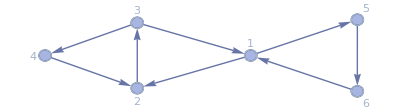

```mathematica
ResourceFunction["WolframModelPlot"][{{1,2},{3,1},{2,3},{3,4},{4,2},{1,5},{6,1},{5,6}},VertexLabels->Automatic]
```

```mathematica
ResourceFunction["MultiwaySystem"]["WolframModel"->{rule},{{{1,2},{3,1},{2,3},{3,4},{4,2},{1,5},{6,1},{5,6}}},2,"EvolutionCausalGraph",VertexSize->1]
```

-Graphics-

```mathematica
rule ={ {1,2},{2,3},{3,1}}->{{1,4}}
```

{{1,2},{2,3},{3,1}}→{{1,4}}

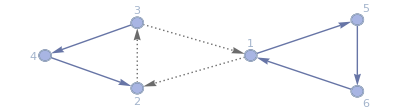
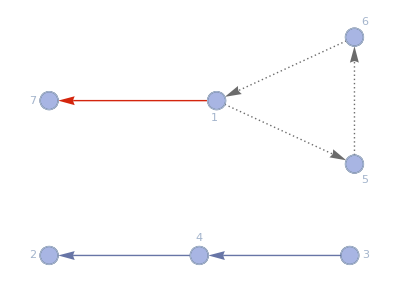
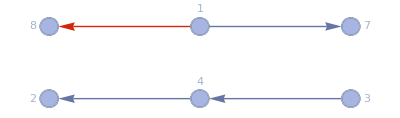

```mathematica
ResourceFunction["WolframModel"][{{1,2},{2,3},{3,1}}->{{1,4}},{{1,2},{3,1},{2,3},{3,4},{4,2},{1,5},{6,1},{5,6}},5]["EventsStatesPlotsList",VertexLabels->Automatic]
```

```mathematica
ResourceFunction["MultiwaySystem"]["WolframModel"-> ]
```

```mathematica
ResourceFunction["CanonicalHypergraph"][{{b,c},{c,d},{d,b},{a,d},{a,b},{a,f},{e,f},{a,e}}]
```

{{1,2},{1,3},{2,3},{3,4},{4,2},{1,5},{1,6},{5,6}}

1:30 - 3:00 (Project) -- complete multiway turing machines

The